3. DOMAČA NALOGA

1. NALOGA

1. pod naloga

```mathematica
v0 = {v0x,v0y};
v0 = {10,3};
GG = 9.81;
H = 10;
a = {0,-GG};
x0 = {0,H};
```

```mathematica
v[t_]:= v0 + a * t
```

```mathematica
v[4]
```

{10,-36.24}

```mathematica
(*z[t_] := {v0[[1]], v0[[2]] - GG * t}
z[4]*)
```

2. pod naloga

```mathematica
x[t_]:=x0+v0*t+(a * t^2)/2
```

```mathematica
x[3]
```

{30,-25.145}

3. pod naloga

```mathematica
SlikaTocke[t_]:={PointSize[0.03],Point[x[t]]};
```

```mathematica
Graphics [SlikaTocke[1]]
```

-Graphics-

Točka v koordniatnem sistemu

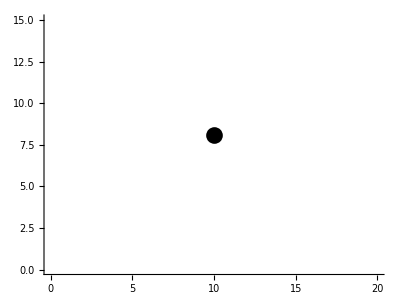

```mathematica
Graphics[SlikaTocke[1],Axes->True,PlotRange->{{0,20},{0,15}}]
```

Manipuliranje s točko

```mathematica
SlikaTocke[t_]:={PointSize[0.03],Point[x[t]]}
Manipulate[Graphics[SlikaTocke[t],Axes->True,PlotRange->{{0,20},{0,20}}],{t,0,3}]
```

4. pod naloga

```mathematica
SlikaVektorja[t_] := Arrow[{x[t],x[t]+v[t]}]
```

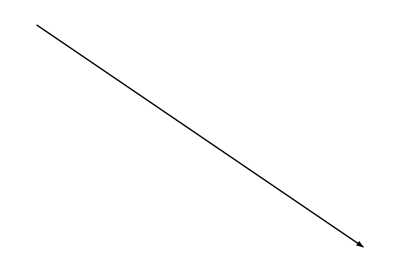

```mathematica
Graphics[SlikaVektorja[1]]
```

5. pod naloga

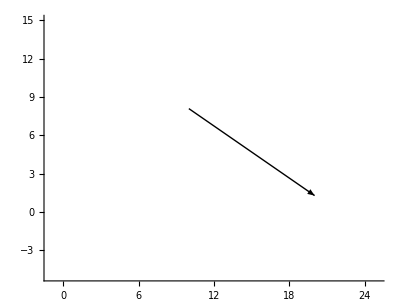

```mathematica
Graphics[SlikaVektorja[1],Axes->True,PlotRange->{{-1,25},{-5,15}},AspectRatio->Full]
```

```mathematica
Manipulate[Graphics[SlikaVektorja[1], Axes->True,PlotRange->{{0,20},{0,15}}],{t,0,5}]
```

6. pod naloga

```mathematica
SlikaVektorja[t_]:={PointSize[0.03],Point[x[t]]};
Manipulate[Graphics[{SlikaTocke[t],Arrow[{x[t],x[t]+v[t]}]},Axes->True,PlotRange->{{0,20},{0,20}},AspectRatio->Automatic], {t, 0 ,5} ]
```

7. pod naloga

```mathematica
X[t][[2]] == 0
```

Part::partw: Part 2 of X[t] does not exist.

X[t]⟦2⟧==0

```mathematica
dolzinaHitrosti = (v0[[1]]^2+v0[[2]]^2)^(1/2)
sinkot =v0[[2]]/ dolzinaHitrosti //N
NajvišjeTočka = dolzinaHitrosti^2* sinkot^2 / (2*GG)+ H
```

√109

0.287348

10.4587

8. pod naloga

```mathematica
časLetaDonajvišjeTočke = 2*dolzinaHitrosti*sinkot/(GG *2)
domet  =dolzinaHitrosti^2 *Sin[2*ArcSin[sinkot]]/GG + H
```

0.30581

16.1162

9. pod naloga

```mathematica
Manipulate[Graphics[{SlikaTocke[t], SlikaVektorja[{ {0,0},v[t]}]},Axes->True, PlotRange->{{-1,18},{-2,12}},AspectRatio->Full], {t, 0, 5}]
```

10. pod naloga

```mathematica
Norm[v[1.7660350319649323]]
```

17.47

2. NALOGA

1. pod naloga

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}]
Slika[Ravnina[n_,v_]] :=Hyperplane[n,v]
```

Ravnina[{-1,-1,-1},{1,1,1}]

2. pod naloga

```mathematica
Format[r_Ravnina] := Graphics3D[Slika[r]]
r =Ravnina[{-1, -1, -1},{1,1,1}]
```

-Graphics3D-

3. pod naloga

```mathematica
Normala[Ravnina[n_,v_]] := n
```

```mathematica
Normala [r111]
```

{-1,-1,-1}

```mathematica
tocka[Ravnina[n_,v_]]:=v
```

```mathematica
rx=Ravnina[{1, 0, 0}, {0, 0, 0}];
SlikaNormale[Ravnina[n_, v_]] :=Arrow[{v, v + n}]
```

```mathematica
Graphics3D[{Slika[r111],SlikaNormale[r111]}]
```

-Graphics3D-

```mathematica
ravnine = {r111, rx};
obeSliki[r_Ravnina] := {Slika[r],SlikaNormale[r]}
Graphics3D[Map[obeSliki, ravnine]]
```

-Graphics3D-

4. pod naloga

```mathematica
rx = Ravnina[{1, 0, 0}, {0, 0, 0}];
ry = Ravnina[{0, 1, 0}, {0, 0, 0}];
rz = Ravnina[{0, 0, 1}, {0, 0, 0}];
ravnine = {rx, ry, rz, r111}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

5. pod naloga

```mathematica
SlikaNormale[Ravnina[n_,v_]] := Arrow[{v,v+n}]
slikeNormal = Map[SlikaNormale, ravnine];
Graphics3D[{slikeNormal}, PlotRange->{{-1, 2}, {-1,2},{-1,2}}]
```

-Graphics3D-

6. pod naloga

```mathematica
slikeRavnin = Map[Slika, ravnine];
Graphics3D[{slikeRavnin, slikeNormal}, PlotRange->{{-1, 4}, {-1, 4},{-1, 4}}]
```

-Graphics3D-

7. pod naloga

```mathematica
Enacba[Ravnina[n_, v_]]:=Module[{a, b, c, d},
a = n[[1]];
b=n[[2]];
c=n[[3]];
d=Dot[n, v];
a*x+b*y+c*z-d==0
]
```

```mathematica
Enacba[r]
```

3-x-y-z==0

8. pod naloga

```mathematica
ResiSistem[sistem_List]:=Solve[{sistem[[1]], sistem[[2]], sistem[[3]]},{x,y,z}]
```

```mathematica
ResiSistem[{Enacba[r], Enacba[rx], Enacba[rz]}]
```

{{x→0,y→3,z→0}}

9. pod naloga

10. pod naloga

```mathematica
Vsebuje[Ravnina[n_,v_],x_,y_,z_,eps_:0.000001]:=Module[{tocka},
tocka = {x,y,z};
If[Dot[n, tocka]<eps, True];
If[Dot[n, tocka]>=eps, False];
]
```

11. pod naloga

```mathematica
Trikotnik[r_Ravnina,tocke_List]:= Graphics3D[Map[Line, Subsets[Vsebuje[r, tocke], 2]]]
```

12. pod naloga

```mathematica
SlikaTrikotnikov[r1_,r2_,r3_,r4_] := Graphics3D[Map[Polygon, Subsets[{r1, r2, r3, r4}], {3}]]
```

3.NALOGA

```mathematica
v={{-1, -1, 0}, {-1, 1, 0}, {0, 0, -(1/Sqrt[2])}, 
  {0, 0, 1/Sqrt[2]}, {1, -1, 0}, {1, 1, 0}};
```

```mathematica
Graphics3D[GraphicsComplex[v,
 Polygon[{{4, 5, 6}, {4,6, 2}, {4, 2, 1}, {4, 1, 5}, {5, 1, 3}, {5, 3, 6}, 
   {3, 1, 2}, {6, 3, 2}}]]]
SlikaNormale[Ravnina[n_, v_]] :=Arrow[{v, v + n}]
```

-Graphics3D-

## 3. Naloga

```mathematica
TriPiramida=Tetrahedron[{{2,4,7},{-1,12,8},{-1,-4,1},{13,-2,7}}];
```

```mathematica
AA={2,4,7};
BB={-1,12,8};
CC={-1,-4,1};
DD={13,-2,7};

VA=BB-AA;
VB=CC-AA;
VC=DD-AA;
```

```mathematica
Produkt[X_,Y_]:=Cross[X,Y]
Razdalja[Vek1_,Vek2_]:=√(Produkt[Vek1,Vek2].Produkt[Vek1,Vek2])/2
Razdalja[VA,VB]
```

(√4345)/2

```mathematica
ProstorninaPiramide[VA_,VB_,VC_]:=Produkt[VA,VB].VC/6
ProstorninaPiramide[VA,VB,VC]
```

-157/3

```mathematica
NN=DD-vektorVisine
```

{8785/869,-15284/4345,45487/4345}

```mathematica
r222=Ravnina[{DD-NN},{NN}];
```

```mathematica
Graphics3D[{{Opacity[0.3],LightBlue,TriPiramida},{PointSize[Large],Red,Point[NN]},{Red,Line[{NN,DD}]}},Axes->True]
```

-Graphics3D-